### Working example

```mathematica
eme=2;
ege=3;
ete =1;
gr=GridGraph[{eme,ege,ete},DirectedEdges->False, VertexLabels->"Name"];
```

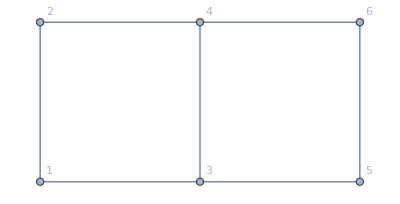

```mathematica
gr
```

```mathematica
(rule=CriticalCongestionSolver2@D2E[Data/.{I1-> 20,I2->200000, U1-> 200,U2->100,U3->0}];)//AbsoluteTiming
```

```mathematica
(rul=CriticalCongestionSolver2[d2egrid=D2E[
AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4},(*FinalCosts=*){{5,U1}/.U1->0},(*SwitchingCostsData=*){{1,2,4,11}, {4,2,1,11}}}]
]])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

u32≤u1&&u25≥u14

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the critical case equations

Expanding critical rules...

EliminateVarsSimplify for the us

Finished with the us!

Finish with the js

{0.173277,<|u1→8/3,u2→2,u3→8/3,u4→4/3,u5→2,u6→8/3,u7→2,u8→4/3,u9→4/3,u10→8/3,u11→4/3,u12→4/3,u13→4/3,u14→0,u15→4/3,u16→2,u17→4/3,u18→4/3,u19→4/3,u20→2/3,u21→0,u22→4/3,u23→0,u24→2/3,u25→0,u26→0,u27→2/3,u28→4/3,u29→2/3,u30→0,u31→8/3,u32→8/3,j1→0,j2→2/3,j3→0,j4→4/3,j5→2/3,j6→0,j7→0,j8→2/3,j9→4/3,j10→0,j11→0,j12→0,j13→0,j14→4/3,j15→2/3,j16→0,j17→0,j18→0,j19→0,j20→2/3,j21→4/3,j22→0,j23→2/3,j24→0,j25→0,j26→4,j27→2/3,j28→0,j29→0,j30→2/3,j31→0,j32→4|>}

```mathematica
us=Values@d2egrid["uvars"];
js=Values@d2egrid["jvars"];
js/.rul//N
us/.rul//N
```

{jt13+jt14+jt15,jt13+jt14+jt15,jt25+jt26+jt27+jt28+jt29,jt25+jt26+jt27+jt28+jt29,jt16+jt17+jt18,jt16+jt17+jt18,jt19+jt20+jt21,jt19+jt20+jt21,jt10+jt11+jt12,jt10+jt11+jt12,jt35+jt36+jt37+jt38+jt39,jt35+jt36+jt37+jt38+jt39,jt40+jt41+jt42+jt43+jt44,jt40+jt41+jt42+jt43+jt44,jt15+jt18+jt21,jt15+jt18+jt21,jt45+jt46+jt47+jt48+jt49,jt45+jt46+jt47+jt48+jt49,jt100+jt103+jt106,jt100+jt103+jt106,jt10+jt11+jt12+jt29-1. jt30-1. jt31-1. jt32-1. jt33+jt39+jt44+jt49,jt10+jt11+jt12+jt29-1. jt30-1. jt31-1. jt32-1. jt33+jt39+jt44+jt49,jt100+jt101+jt102,jt100+jt101+jt102,jt103+jt104+jt105,jt103+jt104+jt105,jt106+jt107+jt108,jt106+jt107+jt108,j29,4.,j31,j32}

{u1,u1,u1,u1,u1,u1,u1,u1,u1,u1,u1,u1,u1,u1,u1,u1,u1,u1,u1,u1,u1,u1,u1,u1,u1,u1,u1,u1,u29,u29,0.,0.}

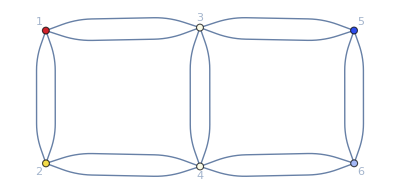

```mathematica
ColorNetworkByValueFunctionOperator[d2egrid][rul]
```

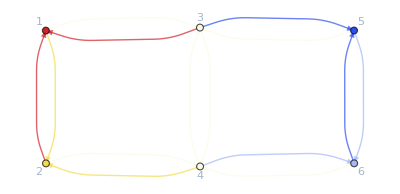

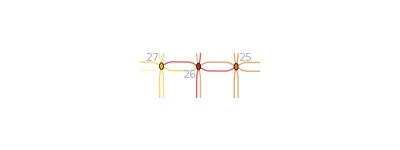

## Other things.....

```mathematica
Terminate[Eqs_][{{system_,rules_},vars_}]:=
Module[{newvars=Drop[vars,1], compvars,groups,subsys,subsyscomplement,subsyseq,subsol ,newsol ={}, newsys, us=Values@Eqs["uvars"],js=Values@Eqs["jvars"],newrules},
compvars = Complement[vars,Take[vars,UpTo[3]]];
(*Print[compvars];*)
groups=GroupBy[List@@system,Function[exp,And@@(FreeQ[#][exp]&/@compvars)]](*True is free of compvars, False only has vars*);
subsys=And@@groups[True];
subsys = Simplify@subsys;
Print["simplify\n",subsys];
subsyseq = getEqual@subsys;
If[subsyseq ===True,
(*there are no equalities in subsyseq, try harder!*)
subsys = Reduce[subsys,Reals];
subsyseq = getEqual@subsys;
Print["first if:\n",subsyseq];
If[subsyseq ===True,
(*give up, but keep the work done.*)
Print[subsys,Simplify@subsys];
newsys = subsys&&And@@groups[False],
newsol=First@Solve@subsyseq;
newrules=Simplify/@Join[rules/.#,#]&@(Association@newsol);
newvars = Variables[Join[us,js]/.newrules]
]
(*newsol=First@Solve@subsyseq;
newrules=Simplify/@Join[rules/.#,#]&@(Association@newsol);
newvars = Variables[Join[us,js]/.newrules]*)
,
Print["it pays to just simplify\n",subsyseq];
newsol=First@Solve@subsyseq;
(*Print["it pays\n",newsol];*)
newrules=Simplify/@Join[rules/.#,#]&@(Association@newsol);
newvars = Variables[Join[us,js]/.newrules];
];
Print[newvars];
{{system/.newrules,newrules},newvars}
]
```

## Other examples

```mathematica
eme=20;
ege=10;
ete =1;
gr=GridGraph[{eme,ege,ete},DirectedEdges->False];
{timegridata,d2egrid}=AbsoluteTiming@D2E[
AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{26,I1}/.I1->4,{177,300}},(*FinalCosts=*){{150,U1}/.U1->0},(*SwitchingCostsData=*){}}]
];
timegridata
(rul=CriticalCongestionSolver2[d2egrid])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the critical case equations

Expanding critical rules...

228.181

EliminateVarsSimplify for the us

Finished with the us!

Finish with the js

{11.046,<|u1→42723465965612233313732868212266957602394664558887076992731/720341816565517713889111663583138418193825058447700769925,u2→24541972811795104134205584817609396090504178143772515069971/411623895180295836508063807761793381825042890541543297100,u3→42723465965612233313732868212266957602394664558887076992731/720341816565517713889111663583138418193825058447700769925,u4→169993918042332137570423851974869888185628069464689010452051/2881367266262070855556446654332553672775300233790803079700,u5→24541972811795104134205584817609396090504178143772515069971/411623895180295836508063807761793381825042890541543297100,u6→42723465965612233313732868212266957602394664558887076992731/720341816565517713889111663583138418193825058447700769925,2960,j1471→0,j1473→0,j1475→10648913438761840597117148542705543927785923935667947043593/1819810905007623698246176834315297056489663305552086155600,j1477→0,j1479→0,j1481→112511571108405667165973489465217084122144243391164471944601/34576407195144850266677359851990644073303602805489636956400|>}
 |  |  |  |

```mathematica
ColorNetworkByValueFunctionOperator[d2egrid][rul]
```

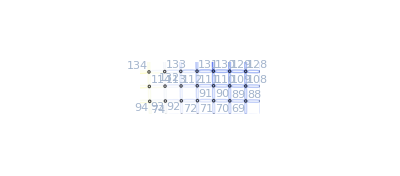

#### Another grid example with different boundary conditions: see way there is a rule like u1->u1.......(this is only for the colornetwork!!!)

```mathematica
eme=10;
ege=10;
ete =1;
gr=GridGraph[{eme,ege,ete},DirectedEdges->True];
{timegridata,d2egrid}=AbsoluteTiming@D2E[
AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{15,I1}/.I1->2000},(*FinalCosts=*){{87,U1}/.U1->0},(*SwitchingCostsData=*){}}]
];
timegridata
(rul=CriticalCongestionSolver2[d2egrid])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the critical case equations

Expanding critical rules...

5.3132

{u1,u363}

EliminateVarsSimplify for the us

all us at the same time!

u363≤2040826938770540/2597098509731+u1&&-5564422973912300/2597098509731+u1≤0&&(jt111==0||2040826938770540/2597098509731+u1-u363==0)&&(jt112==0||2040826938770540/2597098509731+u1-u363==0)&&(jt113==0||2040826938770540/2597098509731+u1-u363==0)&&(2000-jt111-jt112-jt113==0||2040826938770540/2597098509731+u1-u363==0)&&(7751719185377615/7791295529193+jt121+jt122+jt123+jt129-jt130-jt131+jt135+jt229+jt230+jt231-jt235-jt236-jt238-jt239+jt243+jt337+jt338+jt339-jt343-jt344-jt346-jt347+jt351+jt445+jt446+jt447-jt451-jt452-jt454-jt455+jt459+jt553+jt554+jt555-jt559-jt560-jt562-jt563+jt567+jt661+jt662+jt663-jt667-jt668-jt670-jt671+jt675+jt769+jt770+jt771-jt775-jt776-jt778-jt779+jt783-jt883-jt884-jt885==0||5564422973912300/2597098509731-u1==0)&&(133182912635440/236099864521+jt877+jt878+jt879-jt887-jt888-jt889==0||5564422973912300/2597098509731-u1==0)&&(jt894==0||5564422973912300/2597098509731-u1==0)&&(187945722665/426196353-jt121-jt122-jt123-jt129+jt130+jt131-jt135-jt229-jt230-jt231+jt235+jt236+jt238+jt239-jt243-jt337-jt338-jt339+jt343+jt344+jt346+jt347-jt351-jt445-jt446-jt447+jt451+jt452+jt454+jt455-jt459-jt553-jt554-jt555+jt559+jt560+jt562+jt563-jt567-jt661-jt662-jt663+jt667+jt668+jt670+jt671-jt675-jt769-jt770-jt771+jt775+jt776+jt778+jt779-jt783-jt877-jt878-jt879+jt883+jt884+jt885+jt887+jt888+jt889-jt894==0||5564422973912300/2597098509731-u1==0)&&u363≤2040826938770540/2597098509731+u1&&(jt111==0||2040826938770540/2597098509731+u1-u363==0)&&(jt112==0||2040826938770540/2597098509731+u1-u363==0)&&(jt113==0||2040826938770540/2597098509731+u1-u363==0)&&(2000-jt111-jt112-jt113==0||2040826938770540/2597098509731+u1-u363==0)

Finished with the us!

Finish with the js

all us at the same time!

j1≥0&&-384412993907255/7791295529193+j1≥0&&(j1==0||-384412993907255/7791295529193+j1==0)&&j3≥0&&384412993907255/7791295529193+j3≥0&&(j3==0||384412993907255/7791295529193+j3==0)&&j5≥0&&-1260314647955/12426308659+j5≥0&&(j5==0||-1260314647955/12426308659+j5==0)&&j7≥0&&6878038819670/132055856427+j7≥0&&(j7==0||6878038819670/132055856427+j7==0)&&388404951207905/2597098509731+j10≥0&&j10≥0&&(388404951207905/2597098509731+j10==0||j10==0)&&j11≥0&&124999189785310/2597098509731+j11≥0&&(j11==0||124999189785310/2597098509731+j11==0)&&j13≥0&&-1087307103196370/7791295529193+j13≥0&&(j13==0||-1087307103196370/7791295529193+j13==0)&&j15≥0&&-77907750427345/7791295529193+j15≥0&&(j15==0||-77907750427345/7791295529193+j15==0)&&j17≥0&&536007159373375/2597098509731+j17≥0&&(j17==0||536007159373375/2597098509731+j17==0)&&j19≥0&&-2695328581316495/7791295529193+j19≥0&&(j19==0||-2695328581316495/7791295529193+j19==0)&&j21≥0&&87563801505605/410068185747+j21≥0&&(j21==0||87563801505605/410068185747+j21==0)&&j23≥0&&-55690750486370/7791295529193+j23≥0&&(j23==0||-55690750486370/7791295529193+j23==0)&&j25≥0&&37918150907105/236099864521+j25≥0&&(j25==0||37918150907105/236099864521+j25==0)&&j27≥0&&412413248672030/7791295529193+j27≥0&&(j27==0||412413248672030/7791295529193+j27==0)&&j29≥0&&24392686951520/236099864521+j29≥0&&(j29==0||24392686951520/236099864521+j29==0)&&j31≥0&&13525463955585/236099864521+j31≥0&&(j31==0||13525463955585/236099864521+j31==0)&&j33≥0&&390911607154880/7791295529193+j33≥0&&(j33==0||390911607154880/7791295529193+j33==0)&&j35≥0&&414047062245280/7791295529193+j35≥0&&(j35==0||414047062245280/7791295529193+j35==0)&&j37≥0&&390911607154880/7791295529193+j37≥0&&(j37==0||390911607154880/7791295529193+j37==0)&&j39≥0&&-2951395914260/63343866091+j39≥0&&(j39==0||-2951395914260/63343866091+j39==0)&&j41≥0&&4129473432935/43045831653+j41≥0&&(j41==0||4129473432935/43045831653+j41==0)&&j43≥0&&-821024005272385/7791295529193+j43≥0&&(j43==0||-821024005272385/7791295529193+j43==0)&&j45≥0&&4772412144635/43045831653+j45≥0&&(j45==0||4772412144635/43045831653+j45==0)&&j47≥0&&-147101833946090/708299593563+j47≥0&&(j47==0||-147101833946090/708299593563+j47==0)&&j49≥0&&2158552002745/14348610551+j49≥0&&(j49==0||2158552002745/14348610551+j49==0)&&j51≥0&&-1234909311361840/2597098509731+j51≥0&&(j51==0||-1234909311361840/2597098509731+j51==0)&&j53≥0&&584094216415/2265570087+j53≥0&&(j53==0||584094216415/2265570087+j53==0)&&j55≥0&&1415886436316750/2597098509731+j55≥0&&(j55==0||1415886436316750/2597098509731+j55==0)&&j57≥0&&27264504055435/43045831653+j57≥0&&(j57==0||27264504055435/43045831653+j57==0)&&j59≥0&&710605409254965/2597098509731+j59≥0&&(j59==0||710605409254965/2597098509731+j59==0)&&j61≥0&&11382057075685/43045831653+j61≥0&&(j61==0||11382057075685/43045831653+j61==0)&&j63≥0&&1285226041796740/7791295529193+j63≥0&&(j63==0||1285226041796740/7791295529193+j63==0)&&j65≥0&&6955820080885/43045831653+j65≥0&&(j65==0||6955820080885/43045831653+j65==0)&&j67≥0&&772665421111135/7791295529193+j67≥0&&(j67==0||772665421111135/7791295529193+j67==0)&&j69≥0&&1765931733370/14348610551+j69≥0&&(j69==0||1765931733370/14348610551+j69==0)&&j71≥0&&122592050688160/2597098509731+j71≥0&&(j71==0||122592050688160/2597098509731+j71==0)&&j73≥0&&4524510117635/43045831653+j73≥0&&(j73==0||4524510117635/43045831653+j73==0)&&j75≥0&&71044831840/729590367+j75≥0&&(j75==0||71044831840/729590367+j75==0)&&j77≥0&&-82216596878760/2597098509731+j77≥0&&(j77==0||-82216596878760/2597098509731+j77==0)&&j79≥0&&994084481997515/7791295529193+j79≥0&&(j79==0||994084481997515/7791295529193+j79==0)&&j81≥0&&-170912288653595/2597098509731+j81≥0&&(j81==0||-170912288653595/2597098509731+j81==0)&&j83≥0&&1129893673503440/7791295529193+j83≥0&&(j83==0||1129893673503440/7791295529193+j83==0)&&j85≥0&&-260504633548780/2597098509731+j85≥0&&(j85==0||-260504633548780/2597098509731+j85==0)&&j87≥0&&480290257392030/2597098509731+j87≥0&&(j87==0||480290257392030/2597098509731+j87==0)&&j89≥0&&-259517570100990/2597098509731+j89≥0&&(j89==0||-259517570100990/2597098509731+j89==0)&&j91≥0&&2005738819907815/7791295529193+j91≥0&&(j91==0||2005738819907815/7791295529193+j91==0)&&j93≥0&&1014734963500/5758533281+j93≥0&&(j93==0||1014734963500/5758533281+j93==0)&&j95≥0&&2783386118115265/7791295529193+j95≥0&&(j95==0||2783386118115265/7791295529193+j95==0)&&j97≥0&&443555777235365/2597098509731+j97≥0&&(j97==0||443555777235365/2597098509731+j97==0)&&-2102421404608390/7791295529193+j100≥0&&j100≥0&&(-2102421404608390/7791295529193+j100==0||j100==0)&&j101≥0&&328374512792155/2597098509731+j101≥0&&(j101==0||328374512792155/2597098509731+j101==0)&&j103≥0&&1604547227969815/7791295529193+j103≥0&&(j103==0||1604547227969815/7791295529193+j103==0)&&j105≥0&&210900273727720/2597098509731+j105≥0&&(j105==0||210900273727720/2597098509731+j105==0)&&j107≥0&&437107882804405/2597098509731+j107≥0&&(j107==0||437107882804405/2597098509731+j107==0)&&j109≥0&&102509193330635/2597098509731+j109≥0&&(j109==0||102509193330635/2597098509731+j109==0)&&j111≥0&&1144109572483190/7791295529193+j111≥0&&(j111==0||1144109572483190/7791295529193+j111==0)&&j113≥0&&1066215339211265/7791295529193+j113≥0&&(j113==0||1066215339211265/7791295529193+j113==0)&&j115≥0&&-36946866376785/2597098509731+j115≥0&&(j115==0||-36946866376785/2597098509731+j115==0)&&j117≥0&&103467092530/729590367+j117≥0&&(j117==0||103467092530/729590367+j117==0)&&j119≥0&&-201759767288135/7791295529193+j119≥0&&(j119==0||-201759767288135/7791295529193+j119==0)&&j121≥0&&6744822329620/43045831653+j121≥0&&(j121==0||6744822329620/43045831653+j121==0)&&j123≥0&&-216645852914615/7791295529193+j123≥0&&(j123==0||-216645852914615/7791295529193+j123==0)&&j125≥0&&2680951855990/14348610551+j125≥0&&(j125==0||2680951855990/14348610551+j125==0)&&j127≥0&&-301804031840/2597098509731+j127≥0&&(j127==0||-301804031840/2597098509731+j127==0)&&j129≥0&&9889493807120/43045831653+j129≥0&&(j129==0||9889493807120/43045831653+j129==0)&&j131≥0&&230657230702875/2597098509731+j131≥0&&(j131==0||230657230702875/2597098509731+j131==0)&&j133≥0&&1049979414320/3913257423+j133≥0&&(j133==0||1049979414320/3913257423+j133==0)&&j135≥0&&277597718355840/2597098509731+j135≥0&&(j135==0||277597718355840/2597098509731+j135==0)&&j137≥0&&10837568738395/43045831653+j137≥0&&(j137==0||10837568738395/43045831653+j137==0)&&j139≥0&&691899958819865/7791295529193+j139≥0&&(j139==0||691899958819865/7791295529193+j139==0)&&j141≥0&&507543013730/2265570087+j141≥0&&(j141==0||507543013730/2265570087+j141==0)&&j143≥0&&465486745253135/7791295529193+j143≥0&&(j143==0||465486745253135/7791295529193+j143==0)&&j145≥0&&257447992965/1304419141+j145≥0&&(j145==0||257447992965/1304419141+j145==0)&&j147≥0&&76544448906660/2597098509731+j147≥0&&(j147==0||76544448906660/2597098509731+j147==0)&&j149≥0&&7624104812245/43045831653+j149≥0&&(j149==0||7624104812245/43045831653+j149==0)&&j151≥0&&7159385005145/43045831653+j151≥0&&(j151==0||7159385005145/43045831653+j151==0)&&j153≥0&&5047161402995/7791295529193+j153≥0&&(j153==0||5047161402995/7791295529193+j153==0)&&j155≥0&&366625973241625/2597098509731+j155≥0&&(j155==0||366625973241625/2597098509731+j155==0)&&j157≥0&&11061416284405/2597098509731+j157≥0&&(j157==0||11061416284405/2597098509731+j157==0)&&j159≥0&&397558584737000/2597098509731+j159≥0&&(j159==0||397558584737000/2597098509731+j159==0)&&j161≥0&&2063081901255/136689395249+j161≥0&&(j161==0||2063081901255/136689395249+j161==0)&&j163≥0&&1013559082250/5758533281+j163≥0&&(j163==0||1013559082250/5758533281+j163==0)&&j165≥0&&299605222726880/7791295529193+j165≥0&&(j165==0||299605222726880/7791295529193+j165==0)&&j167≥0&&535996274911125/2597098509731+j167≥0&&(j167==0||535996274911125/2597098509731+j167==0)&&j169≥0&&187687539949000/2597098509731+j169≥0&&(j169==0||187687539949000/2597098509731+j169==0)&&j171≥0&&609017205597000/2597098509731+j171≥0&&(j171==0||609017205597000/2597098509731+j171==0)&&j173≥0&&616633637635495/7791295529193+j173≥0&&(j173==0||616633637635495/7791295529193+j173==0)&&j175≥0&&636009641287000/2597098509731+j175≥0&&(j175==0||636009641287000/2597098509731+j175==0)&&j177≥0&&161398798860780/2597098509731+j177≥0&&(j177==0||161398798860780/2597098509731+j177==0)&&j179≥0&&625959221756875/2597098509731+j179≥0&&(j179==0||625959221756875/2597098509731+j179==0)&&j181≥0&&102570951429845/2597098509731+j181≥0&&(j181==0||102570951429845/2597098509731+j181==0)&&j183≥0&&1266977386750/5758533281+j183≥0&&(j183==0||1266977386750/5758533281+j183==0)&&j185≥0&&145519061634880/7791295529193+j185≥0&&(j185==0||145519061634880/7791295529193+j185==0)&&j187≥0&&514052254557000/2597098509731+j187≥0&&(j187==0||514052254557000/2597098509731+j187==0)&&j189≥0&&480455915855375/2597098509731+j189≥0&&(j189==0||480455915855375/2597098509731+j189==0)&&j191≥0&&97844995889120/7791295529193+j191≥0&&(j191==0||97844995889120/7791295529193+j191==0)&&j193≥0&&5536093501855/43045831653+j193≥0&&(j193==0||5536093501855/43045831653+j193==0)&&j195≥0&&70617977642155/2597098509731+j195≥0&&(j195==0||70617977642155/2597098509731+j195==0)&&j197≥0&&5959485177755/43045831653+j197≥0&&(j197==0||5959485177755/43045831653+j197==0)&&j199≥0&&118079684940220/2597098509731+j199≥0&&(j199==0||118079684940220/2597098509731+j199==0)&&j201≥0&&2263278667385/14348610551+j201≥0&&(j201==0||2263278667385/14348610551+j201==0)&&j203≥0&&518668014784505/7791295529193+j203≥0&&(j203==0||518668014784505/7791295529193+j203==0)&&j205≥0&&419761519270/2265570087+j205≥0&&(j205==0||419761519270/2265570087+j205==0)&&j207≥0&&214679975639000/2597098509731+j207≥0&&(j207==0||214679975639000/2597098509731+j207==0)&&j209≥0&&854685939055/3913257423+j209≥0&&(j209==0||854685939055/3913257423+j209==0)&&j211≥0&&586482379045120/7791295529193+j211≥0&&(j211==0||586482379045120/7791295529193+j211==0)&&j213≥0&&10859593766480/43045831653+j213≥0&&(j213==0||10859593766480/43045831653+j213==0)&&j215≥0&&5623493606745/136689395249+j215≥0&&(j215==0||5623493606745/136689395249+j215==0)&&j217≥0&&11844314412880/43045831653+j217≥0&&(j217==0||11844314412880/43045831653+j217==0)&&j219≥0&&45216404562595/2597098509731+j219≥0&&(j219==0||45216404562595/2597098509731+j219==0)&&j221≥0&&317949158910/1304419141+j221≥0&&(j221==0||317949158910/1304419141+j221==0)&&j223≥0&&4066367775455/708299593563+j223≥0&&(j223==0||4066367775455/708299593563+j223==0)&&j225≥0&&9022518960380/43045831653+j225≥0&&(j225==0||9022518960380/43045831653+j225==0)&&j227≥0&&139160763470/729590367+j227≥0&&(j227==0||139160763470/729590367+j227==0)&&j229≥0&&58159629742340/2597098509731+j229≥0&&(j229==0||58159629742340/2597098509731+j229==0)&&j231≥0&&827554034608735/7791295529193+j231≥0&&(j231==0||827554034608735/7791295529193+j231==0)&&j233≥0&&362147432142865/7791295529193+j233≥0&&(j233==0||362147432142865/7791295529193+j233==0)&&j235≥0&&890998274257810/7791295529193+j235≥0&&(j235==0||890998274257810/7791295529193+j235==0)&&j237≥0&&568838603200135/7791295529193+j237≥0&&(j237==0||568838603200135/7791295529193+j237==0)&&j239≥0&&340756381777595/2597098509731+j239≥0&&(j239==0||340756381777595/2597098509731+j239==0)&&j241≥0&&258929284891160/2597098509731+j241≥0&&(j241==0||258929284891160/2597098509731+j241==0)&&j243≥0&&1235610613296185/7791295529193+j243≥0&&(j243==0||1235610613296185/7791295529193+j243==0)&&j245≥0&&302648897997125/2597098509731+j245≥0&&(j245==0||302648897997125/2597098509731+j245==0)&&j247≥0&&1570520865340610/7791295529193+j247≥0&&(j247==0||1570520865340610/7791295529193+j247==0)&&j249≥0&&254905605347840/2597098509731+j249≥0&&(j249==0||254905605347840/2597098509731+j249==0)&&j251≥0&&2108816349680735/7791295529193+j251≥0&&(j251==0||2108816349680735/7791295529193+j251==0)&&j253≥0&&75828553022615/7791295529193+j253≥0&&(j253==0||75828553022615/7791295529193+j253==0)&&j255≥0&&257519015613835/708299593563+j255≥0&&(j255==0||257519015613835/708299593563+j255==0)&&j257≥0&&-130385180652865/7791295529193+j257≥0&&(j257==0||-130385180652865/7791295529193+j257==0)&&j259≥0&&701774686614970/2597098509731+j259≥0&&(j259==0||701774686614970/2597098509731+j259==0)&&j261≥0&&-34082697734215/2597098509731+j261≥0&&(j261==0||-34082697734215/2597098509731+j261==0)&&j263≥0&&1604938844378560/7791295529193+j263≥0&&(j263==0||1604938844378560/7791295529193+j263==0)&&j265≥0&&125804518172135/708299593563+j265≥0&&(j265==0||125804518172135/708299593563+j265==0)&&j267≥0&&79307709625365/2597098509731+j267≥0&&(j267==0||79307709625365/2597098509731+j267==0)&&j269≥0&&55214056160/729590367+j269≥0&&(j269==0||55214056160/729590367+j269==0)&&j271≥0&&14952069794480/236099864521+j271≥0&&(j271==0||14952069794480/236099864521+j271==0)&&j273≥0&&3511066850365/43045831653+j273≥0&&(j273==0||3511066850365/43045831653+j273==0)&&j275≥0&&23702426398895/236099864521+j275≥0&&(j275==0||23702426398895/236099864521+j275==0)&&j277≥0&&1350842315630/14348610551+j277≥0&&(j277==0||1350842315630/14348610551+j277==0)&&j279≥0&&370566035572635/2597098509731+j279≥0&&(j279==0||370566035572635/2597098509731+j279==0)&&j281≥0&&5006036341115/43045831653+j281≥0&&(j281==0||5006036341115/43045831653+j281==0)&&j283≥0&&1068915135500/5758533281+j283≥0&&(j283==0||1068915135500/5758533281+j283==0)&&j285≥0&&6828601070315/43045831653+j285≥0&&(j285==0||6828601070315/43045831653+j285==0)&&j287≥0&&496203212704990/2597098509731+j287≥0&&(j287==0||496203212704990/2597098509731+j287==0)&&j289≥0&&11416844695565/43045831653+j289≥0&&(j289==0||11416844695565/43045831653+j289==0)&&j291≥0&&-19744138148020/236099864521+j291≥0&&(j291==0||-19744138148020/236099864521+j291==0)&&j293≥0&&1446023660585/2265570087+j293≥0&&(j293==0||1446023660585/2265570087+j293==0)&&j295≥0&&-19114254427855/236099864521+j295≥0&&(j295==0||-19114254427855/236099864521+j295==0)&&j297≥0&&3838927987255/14348610551+j297≥0&&(j297==0||3838927987255/14348610551+j297==0)&&j299≥0&&-107779079229240/2597098509731+j299≥0&&(j299==0||-107779079229240/2597098509731+j299==0)&&j301≥0&&7168539701365/43045831653+j301≥0&&(j301==0||7168539701365/43045831653+j301==0)&&j303≥0&&5859184874065/43045831653+j303≥0&&(j303==0||5859184874065/43045831653+j303==0)&&j305≥0&&94598441019840/2597098509731+j305≥0&&(j305==0||94598441019840/2597098509731+j305==0)&&j307≥0&&305835582673120/7791295529193+j307≥0&&(j307==0||305835582673120/7791295529193+j307==0)&&j309≥0&&591422580688865/7791295529193+j309≥0&&(j309==0||591422580688865/7791295529193+j309==0)&&j311≥0&&327875842286720/7791295529193+j311≥0&&(j311==0||327875842286720/7791295529193+j311==0)&&j313≥0&&954765271518260/7791295529193+j313≥0&&(j313==0||954765271518260/7791295529193+j313==0)&&j315≥0&&123388228852565/2597098509731+j315≥0&&(j315==0||123388228852565/2597098509731+j315==0)&&j317≥0&&43684312809185/236099864521+j317≥0&&(j317==0||43684312809185/236099864521+j317==0)&&j319≥0&&419275526556970/7791295529193+j319≥0&&(j319==0||419275526556970/7791295529193+j319==0)&&j321≥0&&758904758167250/2597098509731+j321≥0&&(j321==0||758904758167250/2597098509731+j321==0)&&j323≥0&&400844841928370/7791295529193+j323≥0&&(j323==0||400844841928370/7791295529193+j323==0)&&j325≥0&&133182912635440/236099864521+j325≥0&&(j325==0||133182912635440/236099864521+j325==0)&&j327≥0&&-4715722960955/708299593563+j327≥0&&(j327==0||-4715722960955/708299593563+j327==0)&&j329≥0&&-3539894030557010/7791295529193+j329≥0&&(j329==0||-3539894030557010/7791295529193+j329==0)&&j331≥0&&-2674785542107655/7791295529193+j331≥0&&(j331==0||-2674785542107655/7791295529193+j331==0)&&j335≥0&&-1417802607251615/7791295529193+j335≥0&&(j335==0||-1417802607251615/7791295529193+j335==0)&&j337≥0&&-1137985643210/236099864521+j337≥0&&(j337==0||-1137985643210/236099864521+j337==0)&&j339≥0&&-4555532206740/63343866091+j339≥0&&(j339==0||-4555532206740/63343866091+j339==0)&&j341≥0&&7458195595330/132055856427+j341≥0&&(j341==0||7458195595330/132055856427+j341==0)&&j343≥0&&500182000776745/7791295529193+j343≥0&&(j343==0||500182000776745/7791295529193+j343==0)&&j345≥0&&305835582673120/7791295529193+j345≥0&&(j345==0||305835582673120/7791295529193+j345==0)&&j347≥0&&211237141653280/2597098509731+j347≥0&&(j347==0||211237141653280/2597098509731+j347==0)&&j349≥0&&334625370505845/2597098509731+j349≥0&&(j349==0||334625370505845/2597098509731+j349==0)&&j351≥0&&74902717793395/410068185747+j351≥0&&(j351==0||74902717793395/410068185747+j351==0)&&j353≥0&&607998826667625/2597098509731+j353≥0&&(j353==0||607998826667625/2597098509731+j353==0)&&j355≥0&&1772123527432370/7791295529193+j355≥0&&(j355==0||1772123527432370/7791295529193+j355==0)&&j357≥0&&-300887338225095/2597098509731+j357≥0&&(j357==0||-300887338225095/2597098509731+j357==0)&&j359≥0&&-16495009489495/136689395249+j359≥0&&(j359==0||-16495009489495/136689395249+j359==0)&&j361≥0&&-500182000776745/7791295529193+j361≥0&&(j361==0||-500182000776745/7791295529193+j361==0)

#### Yet another grid example with different boundary conditions: see way there is a rule like u1->u1.......

```mathematica
eme=10;
ege=10;
ete =1;
gr=GridGraph[{eme,ege,ete},DirectedEdges->True];
{timegridata,d2egrid}=AbsoluteTiming@D2E[
AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{12,I1}/.I1->2000},(*FinalCosts=*){{19,U1}/.U1->0},(*SwitchingCostsData=*){}}]
];
timegridata
(rul=CriticalCongestionSolver2[d2egrid])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the critical case equations

Expanding critical rules...

5.70836

{u1,u363}

EliminateVarsSimplify for the us

all us at the same time!

u363==8981662979685750/2597098509731&&u1==8109274780765375/2597098509731&&u363∈ℝ&&u1==(-872388198920375+2597098509731 u363)/2597098509731

Finished with the us!

Finish with the js

all us at the same time!

j1==0&&j3==3096679000/142065451&&j5==0&&j7==928998587719375/2597098509731&&j10==1062831030511500/2597098509731&&j11==77222053993125/2597098509731&&j13==0&&j15==0&&j17==0&&j19==0&&j21==0&&j23==23012464325375/2597098509731&&j25==0&&j27==46231612340625/2597098509731&&j29==0&&j31==0&&j33==0&&j35==0&&j37==0&&j39==815777810121375/2597098509731&&j41==0&&j43==0&&j45==0&&j47==0&&j49==0&&j51==0&&j53==0&&j55==0&&j57==0&&j59==0&&j61==68830709286250/2597098509731&&j63==0&&j65==239136039030250/2597098509731&&j67==0&&j69==573878759406250/2597098509731&&j71==815777810121375/2597098509731&&j73==1612035111376625/2597098509731&&j77==759167421322375/2597098509731&&j79==0&&j81==0&&j83==0&&j85==0&&j87==0&&j89==0&&j91==0&&j93==0&&j95==0&&j97==0&&j100==96052624625/303080699&&j101==82005043075625/2597098509731&&j103==0&&j105==267603075087875/2597098509731&&j107==0&&j109==521565941211250/2597098509731&&j111==0&&j113==849895833035250/2597098509731&&j115==722077541389500/2597098509731&&j117==0&&j119==0&&j121==0&&j123==0&&j125==0&&j127==0&&j129==0&&j131==0&&j133==0&&j135==0&&j137==0&&j139==73591431004000/2597098509731&&j141==0&&j143==227705277034375/2597098509731&&j145==0&&j147==394886097315625/2597098509731&&j149==0&&j151==543904738163625/2597098509731&&j153==557169369810875/2597098509731&&j155==0&&j157==0&&j159==0&&j161==0&&j163==0&&j165==0&&j167==0&&j169==0&&j171==0&&j173==0&&j175==0&&j177==410000/18281&&j179==0&&j181==1230000/18281&&j183==0&&j185==2015750/18281&&j187==0&&j189==2630250/18281&&j191==2854500/18281&&j193==0&&j195==0&&j197==0&&j199==0&&j201==0&&j203==0&&j205==0&&j207==0&&j209==0&&j211==0&&j213==0&&j215==42902238816000/2597098509731&&j217==0&&j219==126641474122375/2597098509731&&j221==0&&j223==202179476874625/2597098509731&&j225==0&&j227==258871609074625/2597098509731&&j229==285740467334875/2597098509731&&j231==0&&j233==0&&j235==0&&j237==0&&j239==0&&j241==0&&j243==0&&j245==0&&j247==0&&j249==0&&j251==0&&j253==29622885047625/2597098509731&&j255==0&&j257==86743676068875/2597098509731&&j259==0&&j261==136836391448250/2597098509731&&j263==0&&j265==173898839596250/2597098509731&&j267==192823963050500/2597098509731&&j269==0&&j271==0&&j273==0&&j275==0&&j277==0&&j279==0&&j281==0&&j283==0&&j285==0&&j287==0&&j289==0&&j291==18468510353250/2597098509731&&j293==0&&j295==53873953657250/2597098509731&&j297==0&&j299==84523573253250/2597098509731&&j301==0&&j303==107063394811625/2597098509731&&j305==118832582220375/2597098509731&&j307==0&&j309==0&&j311==0&&j313==0&&j315==0&&j317==0&&j319==0&&j321==0&&j323==0&&j325==0&&j327==0&&j329==8845713061375/2597098509731&&j331==0&&j333==25760054953625/2597098509731&&j335==0&&j337==40320553095875/2597098509731&&j339==0&&j341==50998584176625/2597098509731&&j343==3096679000/142065451&&j345==0&&j347==0&&j349==0&&j351==0&&j353==0&&j355==0&&j357==0&&j359==0&&j361==0

{0.615397,<|u1→8109274780765375/2597098509731,u2→8052664391966375/2597098509731,u3→8109274780765375/2597098509731,u4→742353197233125/236099864521,u5→8052664391966375/2597098509731,u6→7067055415448000/2597098509731,u7→8052664391966375/2597098509731,u8→8981662979685750/2597098509731,u9→7067055415448000/2597098509731,u10→316011809733500/136689395249,u11→7067055415448000/2597098509731,u12→7144277469441125/2597098509731,u13→316011809733500/136689395249,u14→4987624966765625/2597098509731,u15→316011809733500/136689395249,u16→541635706599625/236099864521,u17→4987624966765625/2597098509731,u18→3994038012920125/2597098509731,u19→4987624966765625/2597098509731,u20→451328409312750/236099864521,u21→3994038012920125/2597098509731,u22→2977438594749250/2597098509731,u23→3994038012920125/2597098509731,u24→4017050477245500/2597098509731,u25→2977438594749250/2597098509731,u26→1914607564237750/2597098509731,u27→2977438594749250/2597098509731,u28→3023670207089875/2597098509731,u29→1914607564237750/2597098509731,u30→928998587719375/2597098509731,u31→1914607564237750/2597098509731,u32→167035046385875/236099864521,u33→928998587719375/2597098509731,u34→872388198920375/2597098509731,u35→928998587719375/2597098509731,u36→0,u37→872388198920375/2597098509731,u38→815777810121375/2597098509731,u39→742353197233125/236099864521,u40→8981662979685750/2597098509731,u41→742353197233125/236099864521,u42→7406717748242000/2597098509731,u43→8981662979685750/2597098509731,u44→7144277469441125/2597098509731,u45→8981662979685750/2597098509731,u46→7369627868309125/2597098509731,u47→7144277469441125/2597098509731,u48→541635706599625/236099864521,u49→7144277469441125/2597098509731,u50→6570398710034875/2597098509731,u51→541635706599625/236099864521,u52→451328409312750/236099864521,u53→541635706599625/236099864521,u54→5718856733565625/2597098509731,u55→451328409312750/236099864521,u56→4017050477245500/2597098509731,u57→451328409312750/236099864521,u58→4895781793154000/2597098509731,u59→4017050477245500/2597098509731,u60→3023670207089875/2597098509731,u61→4017050477245500/2597098509731,u62→4085881186531750/2597098509731,u63→3023670207089875/2597098509731,u64→167035046385875/236099864521,u65→3023670207089875/2597098509731,u66→3262806246120125/2597098509731,u67→167035046385875/236099864521,u68→0,u69→167035046385875/236099864521,u70→2411264269650875/2597098509731,u71→0,u72→815777810121375/2597098509731,u73→0,u74→1612035111376625/2597098509731,u75→0,u76→0,u77→815777810121375/2597098509731,u78→1574945231443750/2597098509731,u79→7406717748242000/2597098509731,u80→7369627868309125/2597098509731,u81→7406717748242000/2597098509731,u82→6684640206852500/2597098509731,u83→7369627868309125/2597098509731,u84→6570398710034875/2597098509731,u85→7369627868309125/2597098509731,u86→14456168592625/5758533281,u87→6570398710034875/2597098509731,u88→5718856733565625/2597098509731,u89→6570398710034875/2597098509731,u90→549893888074875/236099864521,u91→5718856733565625/2597098509731,u92→4895781793154000/2597098509731,u93→5718856733565625/2597098509731,u94→5451253658477750/2597098509731,u95→4895781793154000/2597098509731,u96→4085881186531750/2597098509731,u97→4895781793154000/2597098509731,u98→4813776750078375/2597098509731,u99→4085881186531750/2597098509731,u100→3262806246120125/2597098509731,u101→4085881186531750/2597098509731,u102→378898748146125/236099864521,u103→3262806246120125/2597098509731,u104→2411264269650875/2597098509731,u105→3262806246120125/2597098509731,u106→320946301928000/236099864521,u107→2411264269650875/2597098509731,u108→1612035111376625/2597098509731,u109→2411264269650875/2597098509731,u110→2932830210862125/2597098509731,u111→1612035111376625/2597098509731,u112→1574945231443750/2597098509731,u113→1612035111376625/2597098509731,u114→148496950625/156649889,u115→1574945231443750/2597098509731,u116→208820252075750/236099864521,u117→6684640206852500/2597098509731,u118→14456168592625/5758533281,u119→6684640206852500/2597098509731,u120→6127470837041625/2597098509731,u121→14456168592625/5758533281,u122→549893888074875/236099864521,u123→14456168592625/5758533281,u124→5975827297110250/2597098509731,u125→549893888074875/236099864521,u126→5451253658477750/2597098509731,u127→549893888074875/236099864521,u128→5653946671508000/2597098509731,u129→5451253658477750/2597098509731,u130→4813776750078375/2597098509731,u131→5451253658477750/2597098509731,u132→5223548381443375/2597098509731,u133→4813776750078375/2597098509731,u134→378898748146125/236099864521,u135→4813776750078375/2597098509731,u136→4740185319074375/2597098509731,u137→378898748146125/236099864521,u138→320946301928000/236099864521,u139→378898748146125/236099864521,u140→4241477660611375/2597098509731,u141→320946301928000/236099864521,u142→2932830210862125/2597098509731,u143→320946301928000/236099864521,u144→3758114598242375/2597098509731,u145→2932830210862125/2597098509731,u146→148496950625/156649889,u147→2932830210862125/2597098509731,u148→3327716308177750/2597098509731,u149→148496950625/156649889,u150→208820252075750/236099864521,u151→148496950625/156649889,u152→3005835682575500/2597098509731,u153→208820252075750/236099864521,u154→2854192142644125/2597098509731,u155→6127470837041625/2597098509731,u156→5975827297110250/2597098509731,u157→6127470837041625/2597098509731,u158→5721945007162125/2597098509731,u159→5975827297110250/2597098509731,u160→5653946671508000/2597098509731,u161→5975827297110250/2597098509731,u162→5602159644617500/2597098509731,u163→5653946671508000/2597098509731,u164→5223548381443375/2597098509731,u165→5653946671508000/2597098509731,u166→5367578238654750/2597098509731,u167→5223548381443375/2597098509731,u168→4740185319074375/2597098509731,u169→5223548381443375/2597098509731,u170→5048807876713375/2597098509731,u171→4740185319074375/2597098509731,u172→4241477660611375/2597098509731,u173→4740185319074375/2597098509731,u174→4681938484164375/2597098509731,u175→4241477660611375/2597098509731,u176→3758114598242375/2597098509731,u177→4241477660611375/2597098509731,u178→4299724495521375/2597098509731,u179→3758114598242375/2597098509731,u180→3327716308177750/2597098509731,u181→3758114598242375/2597098509731,u182→3932855102972375/2597098509731,u183→3327716308177750/2597098509731,u184→3005835682575500/2597098509731,u185→3327716308177750/2597098509731,u186→3614084741031000/2597098509731,u187→3005835682575500/2597098509731,u188→2854192142644125/2597098509731,u189→3005835682575500/2597098509731,u190→3379503335068250/2597098509731,u191→2854192142644125/2597098509731,u192→3259717972523625/2597098509731,u193→5721945007162125/2597098509731,u194→5602159644617500/2597098509731,u195→5721945007162125/2597098509731,u196→5436204539827250/2597098509731,u197→5602159644617500/2597098509731,u198→5367578238654750/2597098509731,u199→5602159644617500/2597098509731,u200→11847645311625/5758533281,u201→5367578238654750/2597098509731,u202→5048807876713375/2597098509731,u203→5367578238654750/2597098509731,u204→469581705616375/236099864521,u205→5048807876713375/2597098509731,u206→4681938484164375/2597098509731,u207→5048807876713375/2597098509731,u208→4922166402591000/2597098509731,u209→4681938484164375/2597098509731,u210→4299724495521375/2597098509731,u211→4681938484164375/2597098509731,u212→4639036245348375/2597098509731,u213→4299724495521375/2597098509731,u214→3932855102972375/2597098509731,u215→4299724495521375/2597098509731,u216→394784248576125/236099864521,u217→3932855102972375/2597098509731,u218→3614084741031000/2597098509731,u219→3932855102972375/2597098509731,u220→369045143372250/236099864521,u221→3614084741031000/2597098509731,u222→3379503335068250/2597098509731,u223→3614084741031000/2597098509731,u224→3816264217905625/2597098509731,u225→3379503335068250/2597098509731,u226→3259717972523625/2597098509731,u227→3379503335068250/2597098509731,u228→219456839625/156649889,u229→3259717972523625/2597098509731,u230→322314403623500/236099864521,u231→5436204539827250/2597098509731,u232→11847645311625/5758533281,u233→5436204539827250/2597098509731,u234→5243380576776750/2597098509731,u235→11847645311625/5758533281,u236→469581705616375/236099864521,u237→11847645311625/5758533281,u238→5169389195946625/2597098509731,u239→469581705616375/236099864521,u240→4922166402591000/2597098509731,u241→469581705616375/236099864521,u242→5028562370331875/2597098509731,u243→4922166402591000/2597098509731,u244→4639036245348375/2597098509731,u245→4922166402591000/2597098509731,u246→4835422726522125/2597098509731,u247→4639036245348375/2597098509731,u248→394784248576125/236099864521,u249→4639036245348375/2597098509731,u250→4609413360300750/2597098509731,u251→394784248576125/236099864521,u252→369045143372250/236099864521,u253→394784248576125/236099864521,u254→4372249619385000/2597098509731,u255→369045143372250/236099864521,u256→3816264217905625/2597098509731,u257→369045143372250/236099864521,u258→4146240253163625/2597098509731,u259→3816264217905625/2597098509731,u260→219456839625/156649889,u261→3816264217905625/2597098509731,u262→3953100609353875/2597098509731,u263→219456839625/156649889,u264→322314403623500/236099864521,u265→219456839625/156649889,u266→3812273783739125/2597098509731,u267→322314403623500/236099864521,u268→3738282402909000/2597098509731,u269→5243380576776750/2597098509731,u270→5169389195946625/2597098509731,u271→5243380576776750/2597098509731,u272→465867999505125/236099864521,u273→5169389195946625/2597098509731,u274→5028562370331875/2597098509731,u275→5169389195946625/2597098509731,u276→276917335000/142065451,u277→5028562370331875/2597098509731,u278→4835422726522125/2597098509731,u279→5028562370331875/2597098509731,u280→4944038797078625/2597098509731,u281→4835422726522125/2597098509731,u282→4609413360300750/2597098509731,u283→4835422726522125/2597098509731,u284→434686252078625/236099864521,u285→4609413360300750/2597098509731,u286→4372249619385000/2597098509731,u287→4609413360300750/2597098509731,u288→417358622722500/236099864521,u289→4372249619385000/2597098509731,u290→4146240253163625/2597098509731,u291→4372249619385000/2597098509731,u292→4390718129738250/2597098509731,u293→4146240253163625/2597098509731,u294→3953100609353875/2597098509731,u295→4146240253163625/2597098509731,u296→4200114206820875/2597098509731,u297→3953100609353875/2597098509731,u298→3812273783739125/2597098509731,u299→3953100609353875/2597098509731,u300→367056743873375/236099864521,u301→3812273783739125/2597098509731,u302→3738282402909000/2597098509731,u303→3812273783739125/2597098509731,u304→27588250/18281,u305→3738282402909000/2597098509731,u306→3857114985129375/2597098509731,u307→465867999505125/236099864521,u308→276917335000/142065451,u309→465867999505125/236099864521,u310→5067937605757375/2597098509731,u311→276917335000/142065451,u312→4944038797078625/2597098509731,u313→276917335000/142065451,u314→5011327216958375/2597098509731,u315→4944038797078625/2597098509731,u316→434686252078625/236099864521,u317→4944038797078625/2597098509731,u318→4903718243982750/2597098509731,u319→434686252078625/236099864521,u320→417358622722500/236099864521,u321→434686252078625/236099864521,u322→250304669363750/136689395249,u323→417358622722500/236099864521,u324→4390718129738250/2597098509731,u325→417358622722500/236099864521,u326→4582099136886125/2597098509731,u327→4390718129738250/2597098509731,u328→4200114206820875/2597098509731,u329→4390718129738250/2597098509731,u330→4399563842799625/2597098509731,u331→4200114206820875/2597098509731,u332→367056743873375/236099864521,u333→4200114206820875/2597098509731,u334→4225874261774500/2597098509731,u335→367056743873375/236099864521,u336→27588250/18281,u337→367056743873375/236099864521,u338→4077944735703000/2597098509731,u339→27588250/18281,u340→3857114985129375/2597098509731,u341→27588250/18281,u342→3970335762727375/2597098509731,u343→3857114985129375/2597098509731,u344→3913725373928375/2597098509731,u345→5067937605757375/2597098509731,u346→5011327216958375/2597098509731,u347→5011327216958375/2597098509731,u348→4903718243982750/2597098509731,u349→4903718243982750/2597098509731,u350→250304669363750/136689395249,u351→250304669363750/136689395249,u352→4582099136886125/2597098509731,u353→4582099136886125/2597098509731,u354→4399563842799625/2597098509731,u355→4399563842799625/2597098509731,u356→4225874261774500/2597098509731,u357→4225874261774500/2597098509731,u358→4077944735703000/2597098509731,u359→4077944735703000/2597098509731,u360→3970335762727375/2597098509731,u361→3970335762727375/2597098509731,u362→3913725373928375/2597098509731,u363→8981662979685750/2597098509731,u364→8981662979685750/2597098509731,j75→0,j76→2000,j363→0,j364→2000,j102→0,j104→1888119681750/5758533281,j106→0,j108→93269828250/303080699,j110→0,j112→82239201625/5758533281,j114→0,j116→0,j118→164908171578625/2597098509731,j12→0,j120→557169369810875/2597098509731,j122→42809024222750/236099864521,j124→543904738163625/2597098509731,j126→597579110345875/2597098509731,j128→394886097315625/2597098509731,j130→57952446218125/236099864521,j132→227705277034375/2597098509731,j134→645890520471000/2597098509731,j136→73591431004000/2597098509731,j138→57952446218125/236099864521,j14→92418128924625/236099864521,j140→0,j142→597579110345875/2597098509731,j144→0,j146→42809024222750/236099864521,j148→0,j150→164908171578625/2597098509731,j152→0,j154→0,j156→151643539931375/2597098509731,j158→2854500/18281,j16→46231612340625/2597098509731,j160→29261875054750/236099864521,j162→2630250/18281,j164→430398290064625/2597098509731,j166→2015750/18281,j168→43942096579000/236099864521,j170→1230000/18281,j172→498707658463000/2597098509731,j174→410000/18281,j176→43942096579000/236099864521,j178→0,j18→993586953845500/2597098509731,j180→430398290064625/2597098509731,j182→0,j184→29261875054750/236099864521,j186→0,j188→151643539931375/2597098509731,j190→0,j192→0,j194→119785362544625/2597098509731,j196→285740467334875/2597098509731,j198→21325582360250/236099864521,j2→3096679000/142065451,j20→23012464325375/2597098509731,j200→258871609074625/2597098509731,j202→318770361941375/2597098509731,j204→202179476874625/2597098509731,j206→33351762959000/236099864521,j208→126641474122375/2597098509731,j210→382213988643000/2597098509731,j212→42902238816000/2597098509731,j214→33351762959000/236099864521,j216→0,j218→318770361941375/2597098509731,j22→92418128924625/236099864521,j220→0,j222→21325582360250/236099864521,j224→0,j226→119785362544625/2597098509731,j228→0,j230→0,j232→92916504284375/2597098509731,j234→192823963050500/2597098509731,j236→16171752160250/236099864521,j238→173898839596250/2597098509731,j24→0,j240→243232359189125/2597098509731,j242→136836391448250/2597098509731,j244→25739105203875/236099864521,j246→86743676068875/2597098509731,j248→296409511011000/2597098509731,j250→29622885047625/2597098509731,j252→25739105203875/236099864521,j254→0,j256→243232359189125/2597098509731,j258→0,j26→1062831030511500/2597098509731,j260→16171752160250/236099864521,j262→0,j264→92916504284375/2597098509731,j266→0,j268→0,j270→164060711375/5758533281,j272→118832582220375/2597098509731,j274→16434452750/303080699,j276→107063394811625/2597098509731,j278→428247547250/5758533281,j28→0,j280→84523573253250/2597098509731,j282→26375232375/303080699,j284→53873953657250/2597098509731,j286→525861953250/5758533281,j288→18468510353250/2597098509731,j290→26375232375/303080699,j292→0,j294→428247547250/5758533281,j296→0,j298→16434452750/303080699,j30→89600816047125/236099864521,j300→0,j302→164060711375/5758533281,j304→0,j306→0,j308→62222193421375/2597098509731,j310→3096679000/142065451,j312→10753364005125/236099864521,j314→50998584176625/2597098509731,j316→162490024213750/2597098509731,j318→40320553095875/2597098509731,j32→77222053993125/2597098509731,j320→17327629356125/236099864521,j322→25760054953625/2597098509731,j324→200226720209250/2597098509731,j326→8845713061375/2597098509731,j328→17327629356125/236099864521,j330→0,j332→162490024213750/2597098509731,j334→0,j336→10753364005125/236099864521,j338→0,j34→3096679000/142065451,j340→62222193421375/2597098509731,j342→0,j344→0,j346→3096679000/142065451,j348→9782633906875/236099864521,j350→147929526071500/2597098509731,j352→15789961911375/236099864521,j354→182535294086500/2597098509731,j356→15789961911375/236099864521,j358→147929526071500/2597098509731,j36→928998587719375/2597098509731,j360→9782633906875/236099864521,j362→3096679000/142065451,j38→3096679000/142065451,j4→0,j40→0,j42→759167421322375/2597098509731,j44→167035046385875/236099864521,j46→1612035111376625/2597098509731,j48→1186284696845250/2597098509731,j50→573878759406250/2597098509731,j52→90307297286875/236099864521,j54→239136039030250/2597098509731,j56→947562025194750/2597098509731,j58→68830709286250/2597098509731,j6→89600816047125/236099864521,j60→90307297286875/236099864521,j62→0,j64→1186284696845250/2597098509731,j66→0,j68→167035046385875/236099864521,j70→0,j72→0,j74→0,j78→0,j8→0,j80→82239201625/5758533281,j82→722077541389500/2597098509731,j84→93269828250/303080699,j86→849895833035250/2597098509731,j88→1888119681750/5758533281,j9→0,j90→521565941211250/2597098509731,j92→96052624625/303080699,j94→267603075087875/2597098509731,j96→1795788484750/5758533281,j98→82005043075625/2597098509731,j99→0,j1→0,j10→1062831030511500/2597098509731,j100→96052624625/303080699,j101→82005043075625/2597098509731,j103→0,j105→267603075087875/2597098509731,j107→0,j109→521565941211250/2597098509731,j11→77222053993125/2597098509731,j111→0,j113→849895833035250/2597098509731,j115→722077541389500/2597098509731,j117→0,j119→0,j121→0,j123→0,j125→0,j127→0,j129→0,j13→0,j131→0,j133→0,j135→0,j137→0,j139→73591431004000/2597098509731,j141→0,j143→227705277034375/2597098509731,j145→0,j147→394886097315625/2597098509731,j149→0,j15→0,j151→543904738163625/2597098509731,j153→557169369810875/2597098509731,j155→0,j157→0,j159→0,j161→0,j163→0,j165→0,j167→0,j169→0,j17→0,j171→0,j173→0,j175→0,j177→410000/18281,j179→0,j181→1230000/18281,j183→0,j185→2015750/18281,j187→0,j189→2630250/18281,j19→0,j191→2854500/18281,j193→0,j195→0,j197→0,j199→0,j201→0,j203→0,j205→0,j207→0,j209→0,j21→0,j211→0,j213→0,j215→42902238816000/2597098509731,j217→0,j219→126641474122375/2597098509731,j221→0,j223→202179476874625/2597098509731,j225→0,j227→258871609074625/2597098509731,j229→285740467334875/2597098509731,j23→23012464325375/2597098509731,j231→0,j233→0,j235→0,j237→0,j239→0,j241→0,j243→0,j245→0,j247→0,j249→0,j25→0,j251→0,j253→29622885047625/2597098509731,j255→0,j257→86743676068875/2597098509731,j259→0,j261→136836391448250/2597098509731,j263→0,j265→173898839596250/2597098509731,j267→192823963050500/2597098509731,j269→0,j27→46231612340625/2597098509731,j271→0,j273→0,j275→0,j277→0,j279→0,j281→0,j283→0,j285→0,j287→0,j289→0,j29→0,j291→18468510353250/2597098509731,j293→0,j295→53873953657250/2597098509731,j297→0,j299→84523573253250/2597098509731,j3→3096679000/142065451,j301→0,j303→107063394811625/2597098509731,j305→118832582220375/2597098509731,j307→0,j309→0,j31→0,j311→0,j313→0,j315→0,j317→0,j319→0,j321→0,j323→0,j325→0,j327→0,j329→8845713061375/2597098509731,j33→0,j331→0,j333→25760054953625/2597098509731,j335→0,j337→40320553095875/2597098509731,j339→0,j341→50998584176625/2597098509731,j343→3096679000/142065451,j345→0,j347→0,j349→0,j35→0,j351→0,j353→0,j355→0,j357→0,j359→0,j361→0,j37→0,j39→815777810121375/2597098509731,j41→0,j43→0,j45→0,j47→0,j49→0,j5→0,j51→0,j53→0,j55→0,j57→0,j59→0,j61→68830709286250/2597098509731,j63→0,j65→239136039030250/2597098509731,j67→0,j69→573878759406250/2597098509731,j7→928998587719375/2597098509731,j71→815777810121375/2597098509731,j73→1612035111376625/2597098509731,j77→759167421322375/2597098509731,j79→0,j81→0,j83→0,j85→0,j87→0,j89→0,j91→0,j93→0,j95→0,j97→0|>}

```mathematica
ColorNetworkByValueFunctionOperator[d2egrid][rul]
```

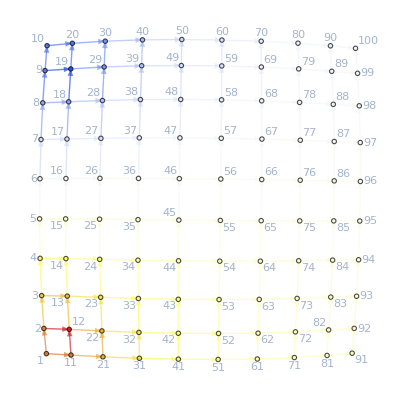

### Copy of the relevant functions

#### CleanEqualities

```mathematica
CleanEqualities[system_]:=
CleanEqualities[{system,{}}]
CleanEqualities[{system_,rules_}]:=
FixedPoint[EqEliminator,{system,rules}]
```

EqEliminator

```mathematica
EqEliminator[{True,rules_}]:=
{True,Simplify/@rules}
EqEliminator[{system_Or,rules_}]:=
{Simplify@system,Simplify/@rules}
EqEliminator[{system_GreaterEqual,rules_}]:=
{Simplify@system,Simplify/@rules}
EqEliminator[{system_LessEqual,rules_}]:=
{Simplify@system,Simplify/@rules}
EqEliminator[{system_Inequality,rules_}]:=
{Simplify@system,Simplify/@rules}
EqEliminator[{False,rules_}]:=
{False,rules}
EqEliminator[{system_,rules_List}]:=
EqEliminator[{system,Association[rules]}]
EqEliminator[{system_Equal,rules_Association}]:=
Module[{newrules},newrules=First@Solve[system];
newrules=Association[newrules];
{True,Join[rules/.newrules,newrules]}
]
EqEliminator[{system_And,rules_Association}]:=
Module[{EE,ON,newrules},(*separate equalities from the rest*)
EE=Select[system,(Head[#]===Equal)&];
If[EE===True,Return[{system,rules}]];
newrules=Solve[EE]//Quiet;(*The reason we use Quiet is:Solve::svars:Equations may not give solutions for all "solve" variables.*)
ON=Select[system,(Head[#]=!=Equal)&];
newrules=First@newrules;
newrules=Join[rules,Association@newrules];
{ON/.newrules,newrules/.newrules}
]
```

#### EliminateVars

```mathematica
EliminateVars[{{system_,rules_},vars_}]:=
FixedPoint[EliminateVarsStep,{{system,rules},vars}]
```

```mathematica
EliminateVarsStep[{{system_,rules_},vars_}]:=
Module[{var,subsys,subsyscomplement,position,newsys,newrules},var=SelectFirst[vars,!FreeQ[#][system]&];
Print[var];
If[Head[var]===Missing,
{{system,rules},{}},
position=First@FirstPosition[vars,var];
subsys=Select[system,Function[x,!FreeQ[var][x]]];
subsyscomplement=Select[system,Function[x,FreeQ[var][x]]];
subsys=Simplify[subsys];
newsys=subsys&&subsyscomplement;
{newsys,newrules}=CleanEqualities[{newsys,rules}];
{{newsys,newrules},Drop[vars,position]}
]
]
```